```mathematica
data1={{"int", 0.035}, {"Integer", 0.056},{"long",0.052},{"Long",0.063}, {"float", 0.086}, {"Float", 0.220}, {"double", 0.085},{"Double", 0.199},{"short", 0.040}, {"Short", 0.068}, {"bool", 0.034}, {"Boolean", 0.054}, {"char", 0.033},{"Character", 0.075}, {"byte", 0.037}, {"Byte", 0.069}};
```

```mathematica
data2={{"int", 0.073}, {"Integer", 0.076},{"long",0.077},{"Long",0.104}, {"float", 0.129}, {"Float", 0.380}, {"double", 0.110},{"Double", 0.373},{"short", 0.082}, {"Short", 0.145}, {"bool", 0.093}, {"Boolean", 0.178}, {"char", 0.122},{"Character", 0.169}, {"byte", 0.060}, {"Byte", 0.105}};
```

```mathematica
data3 = {{"int", 0.055}, {"Integer", 0.113},{"long",0.069},{"Long",0.088}, {"float", 0.083}, {"Float", 0.173}, {"double", 0.127},{"Double", 0.228},{"short", 0.037}, {"Short", 0.071}, {"bool", 0.041}, {"Boolean", 0.055}, {"char", 0.053},{"Character", 0.087}, {"byte", 0.051}, {"Byte", 0.085}};
```

```mathematica
data4 = {{"bool",0.036},{"Bool",0.092},{"byte",0.048},{"Byte",0.102},{"char",0.045},{"Char",0.075},{"double",0.109},{"Double",0.392},{"float",0.101},{"Float",0.298},{"int",0.045},{"Int",0.084},{"long",0.074},{"Long",0.076},{"short",0.055},{"Short",0.094}}
```

{{bool,0.036},{Bool,0.092},{byte,0.048},{Byte,0.102},{char,0.045},{Char,0.075},{double,0.109},{Double,0.392},{float,0.101},{Float,0.298},{int,0.045},{Int,0.084},{long,0.074},{Long,0.076},{short,0.055},{Short,0.094}}

```mathematica
data = data4
```

{{bool,0.036},{Bool,0.092},{byte,0.048},{Byte,0.102},{char,0.045},{Char,0.075},{double,0.109},{Double,0.392},{float,0.101},{Float,0.298},{int,0.045},{Int,0.084},{long,0.074},{Long,0.076},{short,0.055},{Short,0.094}}

```mathematica
colors = {Lighter[Orange], Lighter[Green,.5], Lighter[Red, 0.5], Lighter[Blue, 0.5], Lighter[Yellow,0.4], Lighter[Magenta, 0.4], Lighter[Purple,0.2], Lighter[Cyan,0.4]}
doubleColors = Flatten[{#,#} &  /@ colors]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

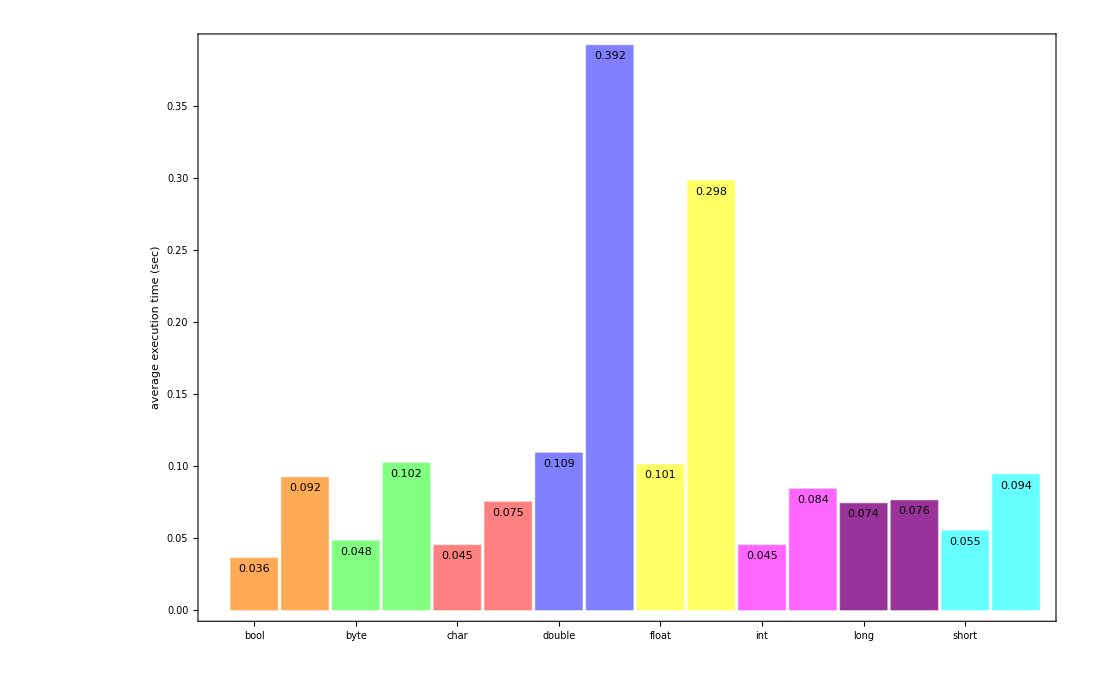

```mathematica
plot = BarChart[Labeled[#[[2]], #[[2]], Top] & /@ data, ChartLabels->(Text[Style[#[[1]],20]] & /@ data),BarSpacing->0.08, ChartStyle ->doubleColors, ImageSize->1100, Axes->False, Frame->{{True, False}, {True, False}}, FrameStyle->Directive[Black,20, Thickness[0.003]], FrameLabel->{None,"average execution time (sec)"}]
```

```mathematica
Export[ "f:\\Users\\Andrea\\Documents\\baeldung\\plot-benchmark-primitive-wrapper-3.gif", plot, ImageSize->1000, ImageResolution->300]
```

f:\Users\Andrea\Documents\baeldung\plot-benchmark-primitive-wrapper-3.gif

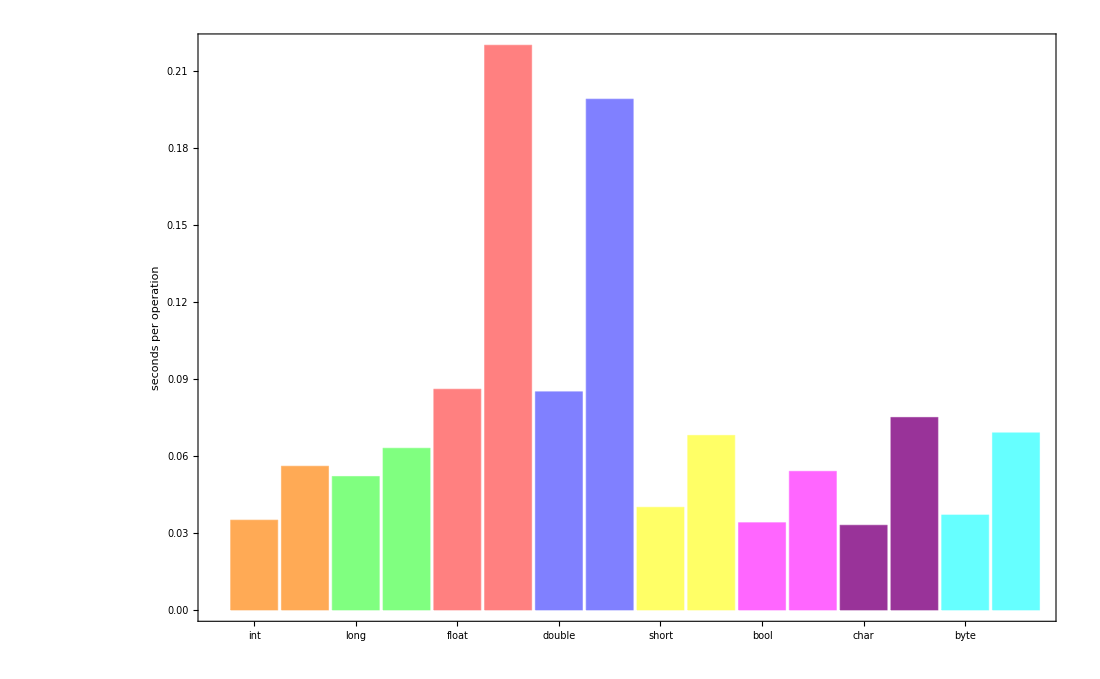

```mathematica
plot = BarChart[#[[2]] & /@ data1, ChartLabels->(Text[Style[#[[1]],20]] & /@ data1),BarSpacing->0.08, ChartStyle ->doubleColors, ImageSize->1100, Axes->False, Frame->{{True, False}, {True, False}}, FrameStyle->Directive[Black,20, Thickness[0.003]], FrameLabel->{None,"seconds per operation"}]
```

```mathematica
Labeled[#[[2]], #[[1]], Top] & /@ data
```

{0.036bool,0.092Bool,0.048byte,0.102Byte,0.045char,0.075Char,0.109double,0.392Double,0.101float,0.298Float,0.045int,0.084Int,0.074long,0.076Long,0.055short,0.094Short}